```mathematica
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
rosenbrok[{x_,y_}]:=(1-x)^2+100(y-x^2)^2;
```

```mathematica
GradientDescent[{X0_,Y0_}, func_,ϵ_]:=Module[{point,direction,step,points={},funcvalues={},norms={},funcprevpoint,funcpoint},
point= {X0,Y0};
funcprevpoint=func[point];
funcpoint = func[point + {1,1}];
AppendTo[points,point];
AppendTo[funcvalues,func[point]];
direction = -Grad[func[{x,y}],{x,y}]/.{x->X0,y->Y0};
While [Norm[funcpoint-funcprevpoint] >ϵ,
step = NArgMin[func[point + α*direction],α];
funcprevpoint=func[point];
point = point + step * direction;
funcpoint = func[point];
AppendTo[points,point];
AppendTo[funcvalues,funcpoint];
AppendTo[norms,Norm[funcprevpoint - funcpoint]];
direction = -Grad[func[{x,y}],{x,y}]/.{x->point[[1]],y->point[[2]]};
];
{points}~Join~{funcvalues}~Join~{norms}
]
```

```mathematica
eps = 10^(-3);
```

```mathematica
Res=GradientDescent[{2,2}, rosenbrok,eps];
points = Res[[1]];
fValues = Res[[2]];
norms = Res[[3]];
func=rosenbrok;
Print[points[[-1]]];
```

{1.29537,1.6759}

```mathematica
Res=GradientDescent[{-2 √5,1}, f,eps];
points = Res[[1]];
fValues = Res[[2]];
norms = Res[[3]];
func=f;
Print[points[[-1]]];
```

{-2.2377,-4.46814}

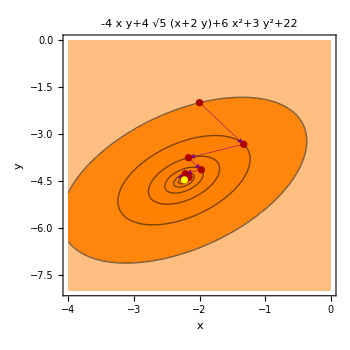

```mathematica
ContourPlot[func[{x,y}],{x,-4,0},{y,-8,0},Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,(*траектория поиска точки минимума*)Epilog->{Purple,Thickness[0.001],Arrowheads[.04],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}]
```

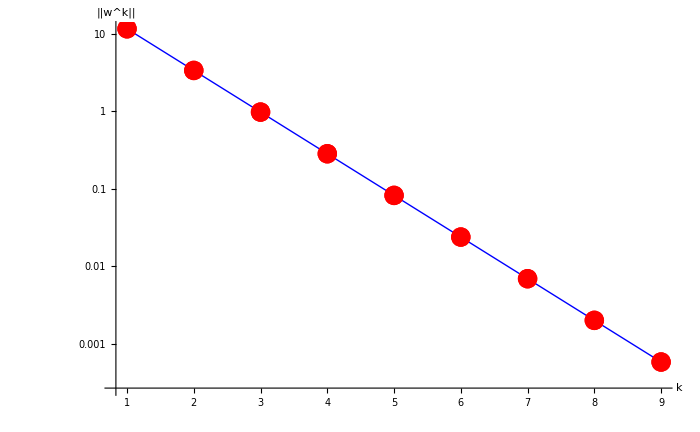

```mathematica
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
```